# Tutorial on the Black Hole Perturbation Toolkit

In this tutorial we will look at various packages from the BHPToolkit. We will:

Use the KerrGeodesics package to explore geodesics of the Kerr spacetime

Use the Teukolsky package to compute the fluxes of gravitational-wave energy for a point mass on a circular orbit in Schwarzschild spacetime, and use them to compute an adiabatic binary black hole inspiral and its associated waveform. We will then compare this to an NR waveform.

We will briefly mention new second-order in the mass ratio results and comparison to NR.

We will quasi-circular inspirals using high-order PN series

We will compute eccentric inspirals using high-order PN series

We will explore (in Python) the Fast EMRI Waveforms package

## Installation

The first step is to install the Mathematica packages provided by the Black Hole Perturbation Toolkit. We recommend that you do so via the Paclet server using the instructions below.

Add the Black Hole Perturbation Toolkit paclet server to Mathematica’s list of paclet servers:

```mathematica
If[$VersionNumber≥12.1,
PacletSiteRegister["https://pacletserver.bhptoolkit.org","Black Hole Perturbation Toolkit Paclet Server"],
PacletSiteAdd["http://pacletserver.bhptoolkit.org","Black Hole Perturbation Toolkit Paclet Server"]
]
```

PacletSiteObject[<|URL→https://pacletserver.bhptoolkit.org,Name→Black Hole Perturbation Toolkit Paclet Server,Local→False,Type→Server|>]

Get an updated list of packages available on the server:

```mathematica
If[$VersionNumber≥12.1,
PacletSiteUpdate["https://pacletserver.bhptoolkit.org"],
PacletSiteUpdate["http://pacletserver.bhptoolkit.org"]
]
```

PacletSiteObject[<|URL→https://pacletserver.bhptoolkit.org,Name→Black Hole Perturbation Toolkit Paclet Server,Local→False,Type→Server|>]

Install the paclets:

```mathematica
PacletInstall["GeneralRelativityTensors"];
PacletInstall["KerrGeodesics"];
PacletInstall["SpinWeightedSpheroidalHarmonics"];
PacletInstall["ReggeWheeler"];
PacletInstall["Teukolsky"];
PacletInstall["PostNewtonianSelfForce"];
```

If a new version of a package is released and you would like to update, just run steps 2 and 3 above again and the latest available version will be installed.

## Geodesics of Kerr spacetime

Let’s first take a look at the KerrGeodesics package.

```mathematica
<<KerrGeodesics`
```

```mathematica
?KerrGeo*
```

The orbital parameters are:
 - a: adimensionalized spin of the black hole
 - p: the semi-latus rectum
 - e: the orbital eccentricity
 - x: Cos[θ_inc] where θ_inc is the maximum inclination angle obtained during the orbital motion as measured from the equatorial plane

```mathematica
KerrGeoConstantsOfMotion[a,p,e,x];
KerrGeoFrequencies[a,p,e,x];
```

There is a general function that computes all the above and the orbital trajectory. The output of this function is also used as input for the later perturbation theory calculations.

```mathematica
orbit=KerrGeoOrbit[0.998,3,0.6,Cos[π/4]];
```

```mathematica
{tp,rp,θp,φp}=orbit["Trajectory"];
```

```mathematica
Show[ParametricPlot3D[{rp[λ] Sin[θp[λ]] Cos[φp[λ]],rp[λ] Sin[θp[λ]] Sin[φp[λ]],rp[λ] Cos[θp[λ]]},{λ,0,20},ImageSize->700,Boxed->False,Axes->False,PlotStyle->Red,PlotRange->All],Graphics3D[{Black,Sphere[{0,0,0},1+Sqrt[1-0.998^2]]}]]
```

-Graphics3D-

There are also functions to computing special orbits:

```mathematica
KerrGeoISCO[a,1]
```

3+√(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)-√((2-(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))) (4+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3))+2 √(3 a^2+(1+(1-a^2)^(1/3) ((1-a)^(1/3)+(1+a)^(1/3)))^2)))

```mathematica
KerrGeoSeparatrix[0,e,1]
```

6+2 e

```mathematica
KerrGeoSeparatrix[0.9`40,0.6`40,Cos[π/4]]
```

3.7198250209555001989388364053315459233

In the near future we expect to have a package for spinning secondaries (MPD equations)

## Numerical Relativity waveform for comparison

We are going to produce a waveform for a binary black hole inspiral using an adiabatic self-force approximation, and compare it against a similar waveform produced in full Numerical Relativity using the Einstein Toolkit. The adiabatic approximation is valid in the limit where one of the black holes is much larger than the other, so we will choose a configuration where the black holes are very different in size. The public RIT waveform catalog has a 1:15 mass ratio configuration with quite a few gravitational-wave cycles, so let’s use that.

First, we load the gravitational wave strain for the l=2, m=2 spherical harmonic mode:

```mathematica
h22=;
```

This is a 1:15 mass ratio system with the individual masses, m_1 and m_2, of the two black holes as given in the metadata file:

```mathematica
m1=0.937508941265577;
m2=0.0624981715324337;
```

The total mass, M, is the sum of the two constituent masses:

```mathematica
M=m1+m2;
```

We now define the (small) mass ratio ϵ, the large mass ratio q, and the symmetric mass ratio, ν:

```mathematica
ϵ=m2/m1;
q=1/ϵ;
ν=(m1 m2)/(m1+m2)^2;
{q,ϵ,ν}
```

{15.0006,0.0666641,0.0585918}

```mathematica
νq[q_]:=q/(1+q)^2
```

```mathematica
νq[q]
```

0.0585918

We will set up our adiabatic calculation to match this system as closely as possible. To do so we will need to provide initial conditions for the adiabatic equations, namely the initial orbital frequency and phase. One way we obtain the from the numerical relativity data is by measuring the phase and frequency of the (2,2) mode of the waveform and dividing by 2. If you have SimulationTools installed you can do that using the following code.

```mathematica
Needs["SimulationTools`"];
Ωinit=-1/2 Frequency[ToDataTable[h22]][[1]];
ϕinit=-1/2 Phase[ToDataTable[h22]][[1]];
```

Doing so, we get the values below:

```mathematica
Ωinit=0.02810756207135854;
```

```mathematica
ϕinit=0.004042174353145999;
```

These correspond to having an initial separation given by:

```mathematica
r0init=(M Ωinit)^(-2/3)
```

10.8172

## Adiabatic quasi-circular inspiral

In the adiabatic approximation,  we effectively treat the system as a point particle in orbit around a black hole. The orbit will gradually decay due to the loss of energy in the form of gravitational radiation. We can think of this as the point particle not quite following a geodesic of the black hole spacetime, but rather as having a small acceleration away from a geodesic. It therefore satisfies the equations for an accelerated particle:



where the force term on the right hand side is the gravitational self-force. In practice computing the all the components of the self-force is a complex task. Currently the BHPToolkit provides some, but not all, the tools needed to do this. Fortunately, we can use an energy balance law to side step this if we just want so-called adiabatic inspirals.

At leading order (ignoring the force term) we get a relationship between the frequency and radius of the orbit,
Ω= √(M/r_0^3)

```mathematica
Ω=KerrGeoFrequencies[0,r0,0,1]["Ω_ϕ"]
```

r0/(√(r0^5))

We can use the chain rule to get an evolution equation for the frequency, Ω:
dΩ/dt=dΩ/dr_0 dr_0/dE dE/dt

```mathematica
dΩdt=Simplify[D[Ω,r0] D[KerrGeoEnergy[0,r0,0,1],r0]^-1//Simplify,Assumptions->r0>2]Edot
```

-(3 Edot (-3+r0)^(3/2))/((-6+r0) r0)

Conservation of energy tells us that any energy lost from the orbit must exactly balance the energy emitted in gravitational waves. Thus we can write:

Ė=-ℱ_GW 

Putting this together, and using the chain rule we get an evolution equation for the frequency, Ω:

dΩ/dt=(3(r_0-3M)^(3/2))/(M^(3/2)r_0(r_0-6M))ℱ.

```mathematica
dΩdt2=dΩdt/.Edot->-ℱGW
```

(3 (-3+r0)^(3/2) ℱGW)/((-6+r0) r0)

This is a simple ordinary differential equation that we can solve for Ω provided we have the flux, ℱ. We can then integrate this once more to get the orbital phase, ϕ_0 using

dϕ_0/dt= Ω

Finally, we can then write the waveform in a form where it is factored into an amplitude and orbital phase.



(Note that since the orbital phase can differ slightly from the waveform phase, the amplitudes are still complex numbers.)

The key things we need, then, are the flux of gravitational waves,  ℱ, and the amplitudes, h^(1) for a point particle on a circular orbit. The packages in the Toolkit make it very easy to compute these in the frequency domain using the Teukolsky formalism.

### Compute energy flux and asymptotic waveform amplitudes

We can use the Teukolsky package to numerically compute the solutions to the Teukolsky equation. First, we load the package

```mathematica
<<Teukolsky`
```

As an example, let’s consider the (l,m)=(2,2) mode of ψ_4 for a circular orbit of radius r_0=10 about a Schwarzschild black hole.  First, we set the parameters of the case we are considering

```mathematica
𝓈=-2;ℓ=2;𝓂=2;
```

```mathematica
a=0; (* Schwarzschild spacetime *);
e=0;(* Zero eccentricity *);
θinc=0; (* Equatorial orbit *)
n=0;k=0; (* Circular orbits don't have frequencies related to radial or polar motion *)
p=10.0`32;(* Semi-latus rectum is just the orbital radius in this case *)
```

In the circular orbit case the frequency of the spherical harmonic mode is a straightforward multiple of this:

```mathematica
ω=𝓂 Ω;
```

Now, we can use the TeukolskyPointParticleMode function from the Teukolsky package to compute the solution to the Teukolsky equation in this case

```mathematica
orbit=KerrGeoOrbit[a,p,e,Cos[θinc]];
```

```mathematica
ψ4=TeukolskyPointParticleMode[𝓈,ℓ,𝓂,0,0,orbit]
```

TeukolskyMode[…]

From this, we can immediately obtain the contribution to the flux from this mode

```mathematica
ℱ22r10=ψ4["EnergyFlux"]
```

<|ℐ→0.00002684397739551056976339,ℋ→5.654138734536942972182×10^-9|>

We can also obtain the metric perturbation amplitudes from the amplitudes of ψ_4 from the simple relation h^(..)=ψ_4

```mathematica
h22r10=(2ψ4["Amplitudes"]["ℐ"])/ω^2;
```

Now, we could clearly run this for a range of modes and orbital radii, but in interest time let’s load some precomputed data for the (2,2) mode of the amplitude and the total (summed over modes) flux on a grid of r_0 values in the range r_0∈[6,30].

```mathematica
ℱ=Interpolation[,InterpolationOrder->8];
```

```mathematica
hAmp=Interpolation[,InterpolationOrder->8];
```

```mathematica
h22r10
```

(0.0005603203959627083051646-0.0001528804192290814215936 ⅈ) r0^3

```mathematica
hAmp[10]
```

0.56032-0.15288 ⅈ

```mathematica
ℱ[10]
```

0.0000615037

```mathematica
2ℱ22r10["ℐ"]
```

0.00005368795479102113952677

### Compute Inspiral

We are now ready to compute an inspiral by solving the equations above for Ω(t) and ϕ_0(t) and r_0(t)

```mathematica
{Ωsol,ϕsol,r0sol}=NDSolveValue[{
Ω0'[t]==(3 (-3 M+r0[t])^(3/2) ν ℱ[r0[t]])/(M^(3/2) r0[t] (-6 M+r0[t])),
ϕ0'[t]==Ω0[t],
Ω0[t]==Sqrt[M/r0[t]^3],
r0[0]==r0init,
ϕ0[0]==ϕinit,
WhenEvent[r0[t]≤6.01M, "StopIntegration"]},{Ω0,ϕ0,r0},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
```

```mathematica
{tmin,tmax}=r0sol["Domain"][[1]];
```

### Plot solutions

Evolution of r_0

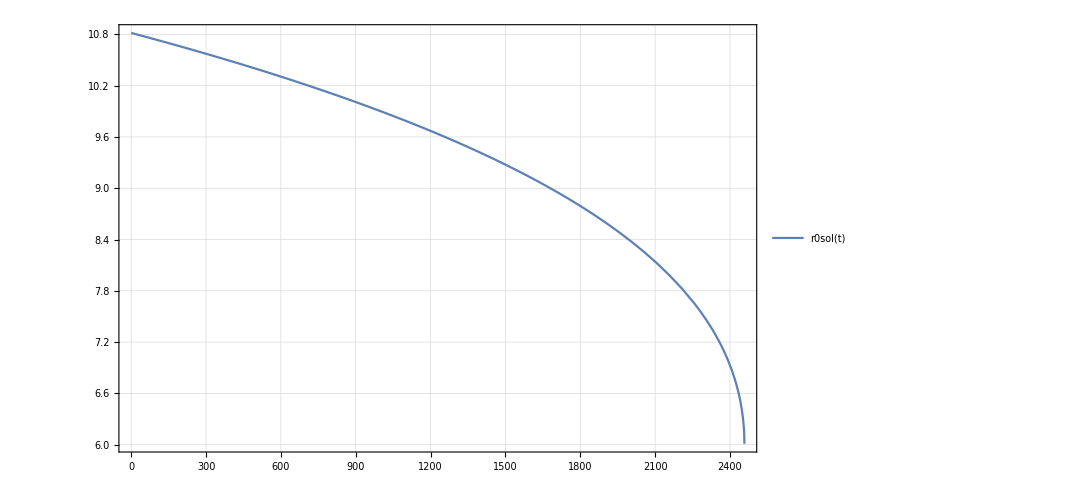

```mathematica
Plot[r0sol[t],{t,tmin,tmax},PlotTheme->"Detailed",ImageSize->800]
```

Evolution of Ω

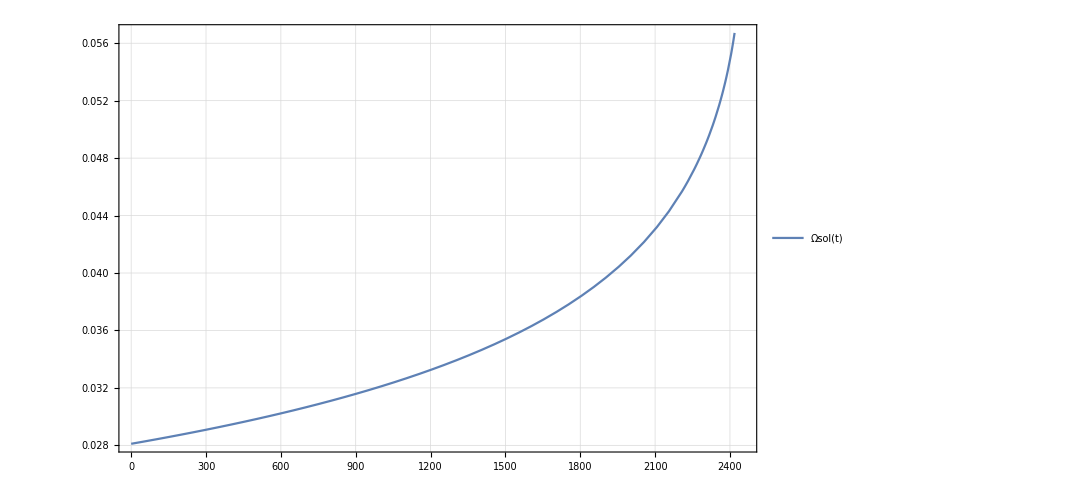

```mathematica
Plot[Ωsol[t],{t,tmin,tmax},PlotTheme->"Detailed",ImageSize->800]
```

Evolution of ϕ_0

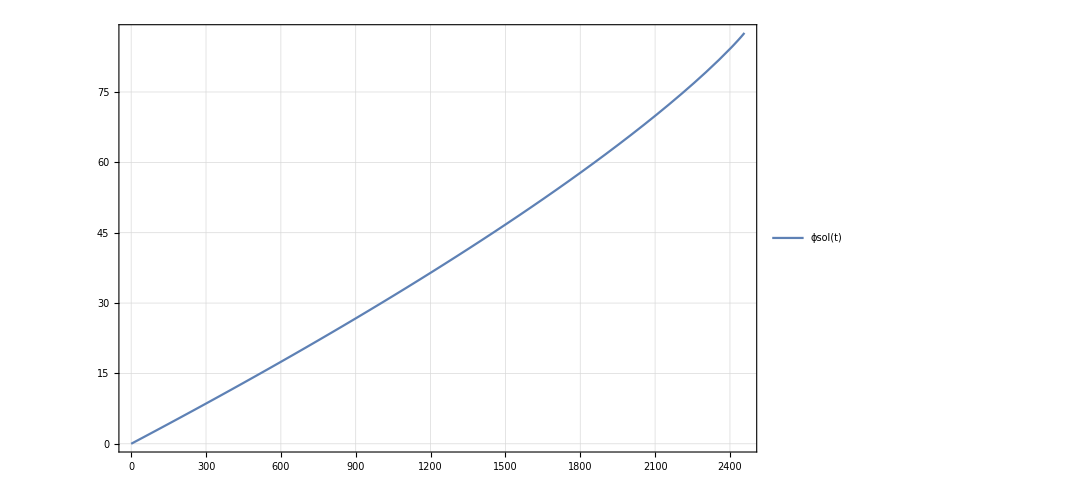

```mathematica
Plot[ϕsol[t],{t,tmin,tmax},PlotTheme->"Detailed",ImageSize->800]
```

## Adiabatic waveform

### Construct waveform from amplitude and phase

We now have everything we need to construct the waveform, we just need to multiply the amplitude by the phase

```mathematica
h[t_]:=ν hAmp[r0sol[t]] ⅇ^(-ⅈ (𝓂 ϕsol[t]+Arg[hAmp[r0sol[0]]]));
```

Let’s plot our waveform alongside the waveform from the Numerical Relativity simulation

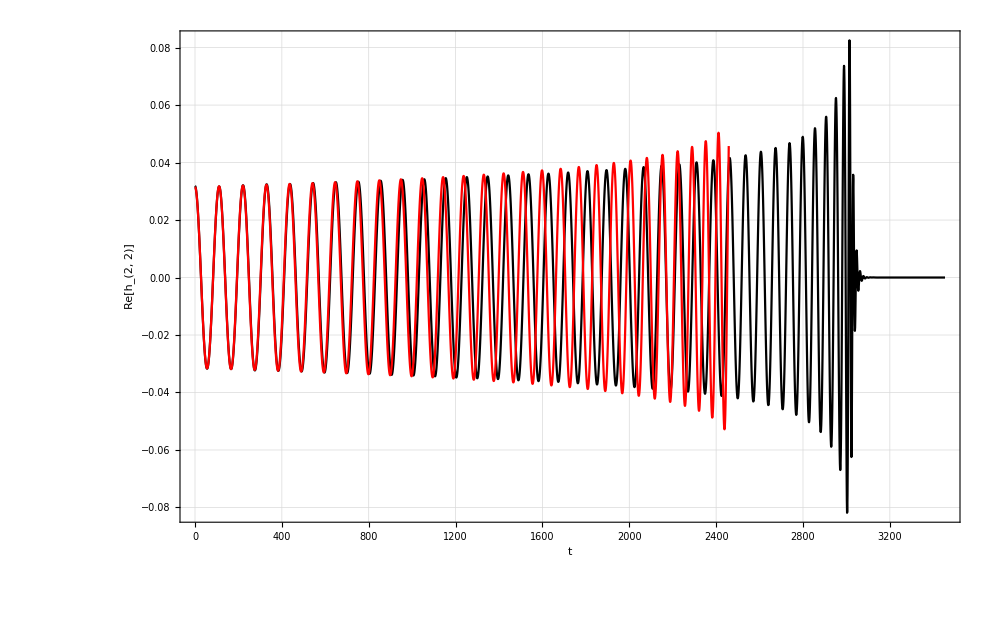

```mathematica
Show[ListLinePlot[Re[h22],PlotTheme->"Detailed",FrameLabel->{"t","Re[h_(2, 2)]"},PlotStyle->Black],Plot[Re[h[t]],{t,tmin,tmax},PlotStyle->Red],PlotRange->All,ImageSize->1000]
```

## Post-adiabatic waveforms

The above result uses first-order (in the mass ratio) fluxes and metric amplitudes to compute a waveform. Very recently it has become possible to compute corrections from the second-order metric perturbation. That is we can write the metric of the binary as:

g_αβ=(ḡ)_αβ+ϵ h_αβ^1+ϵ^2 h_αβ^2

and solve for h_αβ^2 for quasi-circular inspirals into a Schwarzschild black hole. By using a two-timescale expansion where we write

h_αβ^n=∑_m h^(n,m)(Ω,m_1,s_1)e^-imϕ_p

where {Ω,m_1,s_1} evolve on the “slow time” scale t̃=ϵ t, and ϕ_p evolves on the fast timescale, t. Treating t̃ and t as independent variables we can substitute this expansion into the Einstein Field Equations, expand everything onto a basis of tensor spherical harmonics, and regularize the resulting equations. At second-order in the mass ratio the result is a set of coupled ODEs sourced by a non-compact source term formed of quadratic combinations of the first-order metric perturbation, punctures, and “slow-time” derivatives of the first-order metric perturbation. For details of the formulation see: https://arxiv.org/abs/2006.11263.

After many years of work, we have recently solve these equations numerically. They are not quite on the scale of NR simulations but the calculation of individual modes takes a few days on a shared memory 40-core machine (though that the present code is highly inefficient).

The end results are presented in three recent letters: https://arxiv.org/abs/1908.07419, https://arxiv.org/abs/2107.01298, https://arxiv.org/abs/2112.12265. The latter two show quite remarkable agreement with NR simulations for the flux and waveform, respectively, even at mass ratios of 10:1. An example is given below:

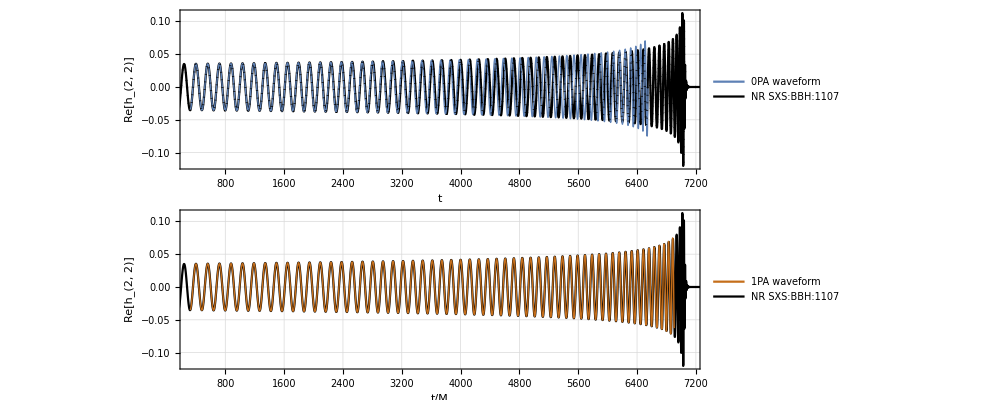

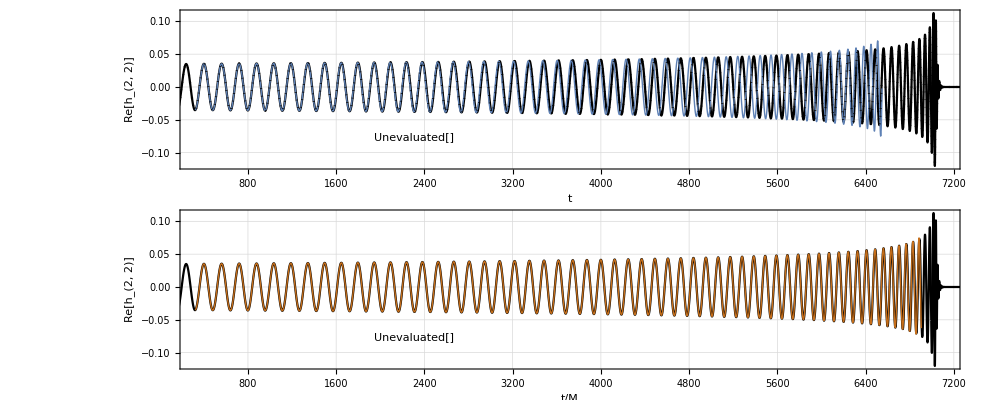

We plan to make the codes to calculate the second-order metric perturbation available on the Black Hole Perturbation Toolkit in the coming year(s).

## Circular inspirals with PN fluxes

In addition to code, the BHPToolkit also stores data. Some of that is numerical data, and some is analytic formula such as high-order post-Newtonian series or regularization parameters.
Let’s look at the PostNewtonianSelfForce package to compute a quasi-circular inspiral.

```mathematica
<<PostNewtonianSelfForce`
```

```mathematica
EdotPN=PostNewtonianExpansion[{"/Schwarzschild/Circular/Flux/Infinity","!-l"}]
```

5         6           13/2             27
                                                                                         32 y    2494 y    128 Pi y                y   (13732992204552647683590179160073585299491645364717826222917476046034799402616358185755542756134625614649556785838454198866352912946773160530080256052774178059455452954799112192 + <<1947>> + 841153594208763538<<146>>000000000 <<1>>)       57/2
PostNewtonianData[<|Name -> Schwarzschild Circular Orbit Infinity Flux, <<3>>, Series -> ----- - ------- + ------------ + <<40>> + -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + O[y]    |>]
                                                                                           5       105          5                                                       204120296690398758308202143901894297290149458343603067294330215619034347563877760075649990602363839146916873832198334827034030146008018780160000000000000000000000

The series are usually very large. We can truncate them easily:

```mathematica
Normal[EdotPN["Series"]+O[y]^8]
```

(32 y^5)/5-(2494 y^6)/105+128/5 π y^(13/2)-(89422 y^7)/2835-8191/105 π y^(15/2)

The post-Newtonian inverse separation parameter y=(M Ω)^(2/3)=M/r_0. Let’s write a function to give us the series to a given order:

```mathematica
ℱPN[r0_,n_]:=Normal[EdotPN["Series"]+O[y]^n]/.y->1/r0
```

Now we can compute the inspiral using different order PN series:

```mathematica
ϕinit
```

0.00404217

```mathematica
Monitor[Do[{ΩsolPN[n],ϕsolPN[n],r0solPN[n]}=NDSolveValue[{
Ω0'[t]==(3 (-3 M+r0[t])^(3/2) νq[q] ℱPN[r0[t],n])/(M^(3/2) r0[t] (-6 M+r0[t])),
ϕ0'[t]==Ω0[t],
Ω0[t]==Sqrt[M/r0[t]^3],
r0[0]==r0init,
ϕ0[0]==ϕinit,
WhenEvent[r0[t]≤6.01M, "StopIntegration"]},{Ω0,ϕ0,r0},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
tmaxPN[n]=ΩsolPN[n]["Domain"][[1,2]];

,{n,6,20}],n];
```

Let’s see how this compares to the numerically computed inspiral:

```mathematica
Manipulate[Show[
Plot[r0solPN[n][t],{t,0,tmaxPN[n]},PlotTheme->"Detailed",PlotLegends->None,ImageSize->800,PlotRange->All,BaseStyle->20],
Plot[r0sol[t],{t,0,tmax},PlotStyle->{Red,Dashed}]
],{n,6,20,1}]
```

We can also compute waveform. Here we will cheat and use the numerical amplitudes as the amplitudes are not (yet!) in the PostNewtonianSelfForce package.

```mathematica
hPN[t_,n_]:=νq[q] hAmp[r0solPN[n][t]] ⅇ^(-ⅈ (𝓂 ϕsolPN[n][t]+Arg[hAmp[r0solPN[n][0]]]));
```

```mathematica
Manipulate[Show[
Plot[Re[h[t]],{t,tmin,tmax},PlotTheme->"Detailed",FrameLabel->{"t","Re[h_(2, 2)]"},PlotStyle->Black,ImageSize->800],
Plot[Re[hPN[t,n]],{t,tmin,tmaxPN[n]},PlotStyle->{Red,Dashed}]
,PlotRange->All],{n,6,20,1}]
```

## Eccentric inspirals with PN fluxes

```mathematica
Clear[y,p,e,ν]
```

Let’s now take a look at an eccentric inspiral. Currently the neither the Teukolsky or ReggeWheeler packages (not any other package in the Toolkit, such as Gremlin) computes fluxes for eccentric orbits. This will change soon. In the meantime, let’s look at using PN series to compute an eccentric inspiral.

```mathematica
{En,L}={"ℰ","ℒ"}/.KerrGeoConstantsOfMotion[0,p,e,1];
```

To get evolution equations for p and e we can write:

Ė=(∂E)/(∂p)ṗ+(∂E)/(∂e)ė     and L̇=(∂L)/(∂p)ṗ+(∂L)/(∂e)ė 

and solve for ṗ and ė.

```mathematica
EoM=Simplify[Solve[{Edot==D[En,p]  pdot+D[En,e]  edot,Ldot==D[L,p] pdot+D[L,e] edot},{ pdot,edot}],Assumptions->{0≤e<1,p>6+2e}][[1]];
```

We now need a PN series for the eccentric orbit energy and angular momentum fluxes. Let’s see what series are available.

```mathematica
PostNewtonianExpansion[]
```

{/Kerr/Circular/Flux/Energy/Horizon,/Kerr/Circular/Flux/Energy/Infinity,/Kerr/Circular/Local/RedShift,/Kerr/Circular/Local/Spin,/Kerr/Generic/Flux/EInfinity-v,/Schwarzschild/Circular/Flux/Horizon,/Schwarzschild/Circular/Flux/Infinity-l2m1,/Schwarzschild/Circular/Flux/Infinity-l2m2,/Schwarzschild/Circular/Flux/Infinity-l3m1,/Schwarzschild/Circular/Flux/Infinity-l3m2,/Schwarzschild/Circular/Flux/Infinity-l3m3,/Schwarzschild/Circular/Flux/Infinity-l4m1,/Schwarzschild/Circular/Flux/Infinity-l4m2,/Schwarzschild/Circular/Flux/Infinity-l4m3,/Schwarzschild/Circular/Flux/Infinity-l4m4,/Schwarzschild/Circular/Flux/Infinity-l5m1,/Schwarzschild/Circular/Flux/Infinity-l5m2,/Schwarzschild/Circular/Flux/Infinity-l5m3,/Schwarzschild/Circular/Flux/Infinity-l5m4,/Schwarzschild/Circular/Flux/Infinity-l5m5,/Schwarzschild/Circular/Flux/Infinity,/Schwarzschild/Circular/Flux/Spin/Infinity-l2m1,/Schwarzschild/Circular/Flux/Spin/Infinity-l2m2,/Schwarzschild/Circular/Flux/Spin/Infinity-l3m1,/Schwarzschild/Circular/Flux/Spin/Infinity-l3m2,/Schwarzschild/Circular/Flux/Spin/Infinity-l3m3,/Schwarzschild/Circular/Flux/Spin/Infinity-l4m1,/Schwarzschild/Circular/Flux/Spin/Infinity-l4m2,/Schwarzschild/Circular/Flux/Spin/Infinity-l4m3,/Schwarzschild/Circular/Flux/Spin/Infinity-l4m4,/Schwarzschild/Circular/Flux/Spin/Infinity-l5m1,/Schwarzschild/Circular/Flux/Spin/Infinity-l5m2,/Schwarzschild/Circular/Flux/Spin/Infinity-l5m3,/Schwarzschild/Circular/Flux/Spin/Infinity-l5m4,/Schwarzschild/Circular/Flux/Spin/Infinity-l5m5,/Schwarzschild/Circular/Flux/Spin/Infinity-l6m1,/Schwarzschild/Circular/Flux/Spin/Infinity-l6m2,/Schwarzschild/Circular/Flux/Spin/Infinity-l6m3,/Schwarzschild/Circular/Flux/Spin/Infinity-l6m4,/Schwarzschild/Circular/Flux/Spin/Infinity-l6m5,/Schwarzschild/Circular/Flux/Spin/Infinity-l6m6,/Schwarzschild/Circular/Flux/Spin/Infinity-l7m1,/Schwarzschild/Circular/Flux/Spin/Infinity-l7m2,/Schwarzschild/Circular/Flux/Spin/Infinity-l7m3,/Schwarzschild/Circular/Flux/Spin/Infinity-l7m4,/Schwarzschild/Circular/Flux/Spin/Infinity-l7m5,/Schwarzschild/Circular/Flux/Spin/Infinity-l7m6,/Schwarzschild/Circular/Flux/Spin/Infinity-l7m7,/Schwarzschild/Circular/Local/RedShift,/Schwarzschild/Circular/Local/Spin/dEdt,/Schwarzschild/Circular/Local/Spin,/Schwarzschild/Circular/Local/Tidal-lambdaB,/Schwarzschild/Circular/Local/Tidal-lambdaE1,/Schwarzschild/Circular/Local/Tidal-lambdaE2,/Schwarzschild/Circular/Local/Tidal-lambdaE3,/Schwarzschild/Eccentric/Flux/EInfinity,/Schwarzschild/Eccentric/Flux/LInfinity,/Schwarzschild/Eccentric/Local/RedShift-ey,/Schwarzschild/Eccentric/Local/RedShift,/Schwarzschild/Eccentric/Local/Spin}

```mathematica
PostNewtonianExpansion[]//Length
```

60

Let’s load the eccentric orbit PN series

```mathematica
EdotEccPN=PostNewtonianExpansion["/Schwarzschild/Eccentric/Flux/EInfinity"];
LdotEccPN=PostNewtonianExpansion["/Schwarzschild/Eccentric/Flux/LInfinity"];
```

We endeavour to include the most up-to-date series. You can queries the series for a reference and authors.

```mathematica
EdotEccPN["References"]
EdotEccPN["Authors"]
```

{Determination of new coefficients in the angular momentum and energy fluxes at infinity to 9PN for eccentric Schwarzschild extreme-mass-ratio inspirals using mode-by-mode fitting, Phys. Rev. D 102, 024047 (2020), arXiv:2005.03044.}

{Christopher Munna, Charles R. Evans, Seth Hopper, Erik Forseth}

```mathematica
Normal[EdotEccPN["Series"]+O[y]^6]
```

((96+292 e^2+37 e^4) y^5)/(15 (1-e^2)^(7/2))

The post-Newtonian inverse separation parameter is still defined via y=(M Ω_ϕ)^(2/3) but now we must use the eccentric orbit Ω_ϕ

```mathematica
ΩϕEcc=KerrGeoFrequencies[0,p,e,1]["Ω_ϕ"];
```

Some series may have additional functions that are needed to use them. These are defined using:

```mathematica
EdotEccPN["ExtraFunctions"];
LdotEccPN["ExtraFunctions"];
```

```mathematica
EdotEccPN3=Block[{highestPower=10},Normal@ReleaseHold[Normal[EdotEccPN["Series"]+O[y]^(5+7)]]]/.y->(M ΩϕEcc)^(2/3);
LdotEccPN3=Block[{highestPower=10},Normal@ReleaseHold[Normal[LdotEccPN["Series"]+O[y]^(7/2+7)]]]/.y->(M ΩϕEcc)^(2/3);
```

```mathematica
EdotEccPNNum[p1_,e1_]:=EdotEccPN3/.{p->p1,e->e1}
LdotEccPNNum[p1_,e1_]:=LdotEccPN3/.{p->p1,e->e1}
```

```mathematica
Clear[p,e,t]
```

```mathematica
pdot2=(pdot/.EoM/.e->e[t]/.p->p[t])/.{Edot->-ν EdotEccPNNum[p[t],e[t]],Ldot->-ν LdotEccPNNum[p[t],e[t]]};
edot2=(edot/.EoM/.e->e[t]/.p->p[t])/.{Edot->-ν EdotEccPNNum[p[t],e[t]],Ldot->-ν LdotEccPNNum[p[t],e[t]]};
```

```mathematica
Clear[p,e]
```

Let’s compute the phase space trajectory

```mathematica
eccTraj=First@Block[{ν=0.15},NDSolve[{
p'[t]==pdot2,
e'[t]==edot2,
p[0]==20.,
e[0]==0.5},{p,e},{t,0,60000}]
]
```

NDSolve::ndsz: At t == 18992.2, step size is effectively zero; singularity or stiff system suspected.

{p→InterpolatingFunction[…],e→InterpolatingFunction[…]}

```mathematica
tmaxEcc=(p/.eccTraj)["Domain"][[1,2]]
```

18992.2

```mathematica
ps=KerrGeoSeparatrix[0,e,1]
```

6+2 e

```mathematica
es=e/.First@Solve[ps==p,e]
```

1/2 (-6+p)

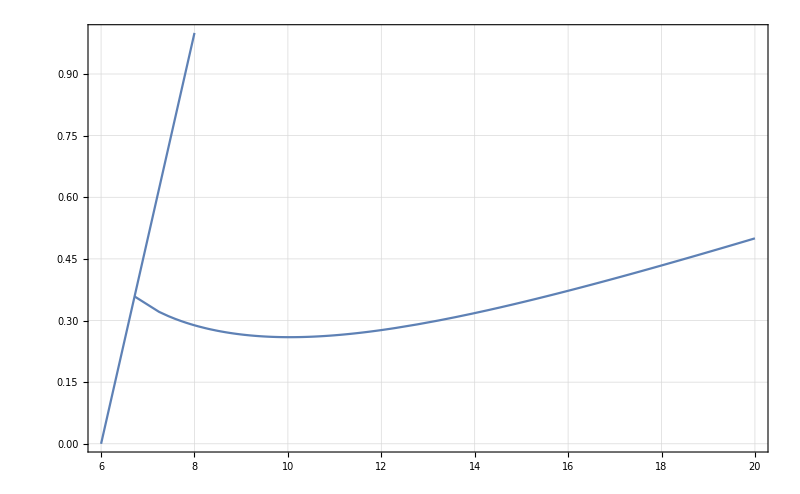

```mathematica
Show[
ParametricPlot[{p[t],e[t]}/.eccTraj,{t,0,tmaxEcc},AspectRatio->1/GoldenRatio,PlotTheme->"Detailed",PlotLegends->None,ImageSize->800],
Plot[es,{p,6,8}],PlotRange->All
]
```

If we want to compute the physical trajectory we need to do a little more. We will introduce the Darwin anomaly parameter, χ, defined via r(χ)=p/(1+e cos(χ)). We will then need dt/dχ and dϕ/dχ. These are given in, e.g., Cutler, Kennefick and Poisson Phys. Rev. D 50, 3816  (1994) to be

```mathematica
dtdχ=(p[t]^2/((p[t]-2-2e[t] Cos[χ[t]])(1+e[t] Cos[χ[t]])^2)Sqrt[((p[t]-2-2e[t])(p[t]-2+2e[t]))/(p[t]-6-2e[t] Cos[χ[t]])]);
dϕdχ=Sqrt[p[t]/(p[t]-6-2e[t] Cos[χ[t]])];
```

```mathematica
eccTraj=First@Block[{ν=0.15},NDSolve[{
p'[t]==pdot2,
e'[t]==edot2,

χ'[t]==dtdχ^-1,
ϕ'[t]==Sqrt[p[t]/(p[t]-6-2e[t] Cos[χ[t]])]χ'[t],

p[0]==20.,
e[0]==0.5,
χ[0]==0,
ϕ[0]==0},{p,e,χ,ϕ},{t,0,60000}]
]
```

NDSolve::ndsz: At t == 18992.2, step size is effectively zero; singularity or stiff system suspected.

{p→InterpolatingFunction[…],e→InterpolatingFunction[…],χ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}

```mathematica
r1[t_]:=p[t]/(1+e[t] Cos[χ[t]])/.eccTraj
```

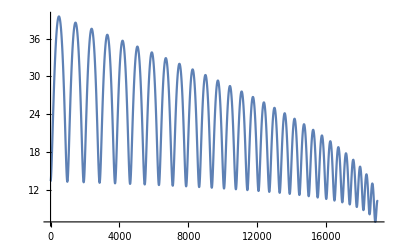

```mathematica
Plot[r1[t],{t,0,tmaxEcc}]
```

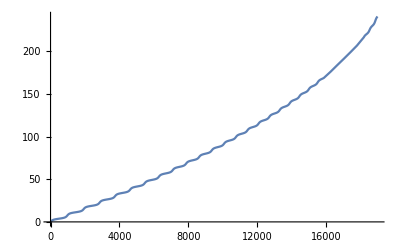

```mathematica
Plot[ϕ[t]/.eccTraj,{t,0,tmaxEcc}]
```

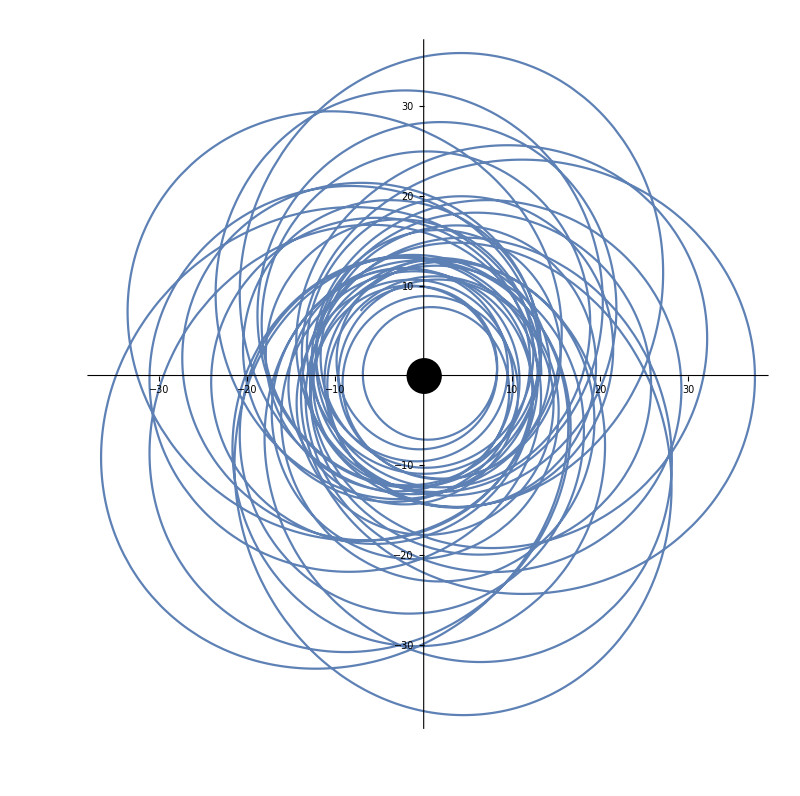

```mathematica
Show[
ParametricPlot[{r1[t]Cos[ϕ[t]],r1[t]Sin[ϕ[t]]}/.eccTraj,{t,0,tmaxEcc},PlotPoints->200,ImageSize->800],
Graphics[Disk[{0,0},2]]
]
```

## Fast EMRI Waveforms

The above is interesting, but it is inaccurate in the strong-field and also quite slow to generate the phase space trajectory. We’ve not attempted to compute the waveform which involves summing over thousands of harmonics at each time step.

Fortunately all the above is resolved by using the Python-based Fast EMRI Waveforms package. This package is a modular framework that is designed to absorb all future self-force calculations and still calculate multi-year long waveforms in less than a second. Let’s explore it now...